## Contour plot for the triaxial rotor

## 3-axis quantization: ℐ_3- maximal M.O.I

## Constans

```mathematica
spinValue=19/2;
j11=11/2;
```

## Functions

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

## Energy Function

```mathematica
Hen[I_,a1_,a2_,a3_,j_,theta_,θ_,ϕ_]:=I^2 Cos[θ]^2(ufct[I,a1,a2,a3,j,theta]-Sin[ϕ]^2-v0fct[I,a1,a2,j,theta]/I Cos[ϕ])+I^2 Sin[ϕ]^2+2I*v0fct[I,a1,a2,j,theta]*Cos[ϕ];
contour[I_,i1_,i2_,i3_,j_,theta_]:=ContourPlot[Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,θ,ϕ],{θ,0,π},{ϕ,-0.2,2π+0.2},PlotLegends->Automatic,Contours->20,FrameStyle->Directive[Black,Thick],FrameLabel->{"θ_3 [rad]","φ_3 [rad]"},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"}];
```

## Numerical factors v_0 and k

```mathematica
Print[N[v0fct[19/2,IF[89],IF[12],j11,-71*π/180]]]
```

-0.170917

```mathematica
Print[N[ufct[19/2,IF[89],IF[12],IF[48],j11,-71*π/180]]]
```

0.081531

### Determine the maximum point (x_1,φ_1)=(0,ArcCos[v_0/I]) - θ_1 coord

```mathematica
Print[N[ArcCos[N[v0fct[19/2,IF[30],IF[15],j11,-11*π/180]]/(19/2)]]]
```

2.05496

### First maximum point P1 for fixed φ_1

```mathematica
minimum[I_,i1_,i2_,i3_,theta_,left_,right_]:=Values@NMinimize[{Hen[I,IF[i1],IF[i2],IF[i3],j11,theta*π/180,π/2,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]];
minimum[19/2,30,15,60,-11,2,4]
```

3.14159

### First maximum point P1 for fixed θ_1

```mathematica
maximum[I_,i1_,i2_,i3_,j_,theta_,left_,right_]:=Values@NMaximize[{Hen[I,IF[i1],IF[i2],IF[i3],j,theta*π/180,π/2,ϕ],ϕ≥left&&ϕ≤right},ϕ][[2,1]];
maximum[19/2,30,15,60,j11,-11,0,3]
```

2.05496

### Draw a point on CP

```mathematica
(*saddle point*)
point1[θ_,text_,x_,y_]:=Graphics[{Red,PointSize[0.021],Point[{π/2,θ}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Red,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
(*maximum point*)
point2[ϕ_,text_,x_,y_]:=Graphics[{Blue,PointSize[0.021],Point[{π/2,ϕ}],Inset[Style[StringTemplate["``"][text],20,Bold,Italic,Blue,FontFamily->"Times New Roman"],Scaled[{x,y}]]}];
```

### New parameters: check the positivity condition

```mathematica
cp[I_]:=Show[contour[I,30,15,60,11/2,-11],point2[maximum[I,30,15,60,11/2,-11,0,3],"M.",0.5,0.4],point2[maximum[I,30,15,60,11/2,-11,3,7],"M.",0.5,0.75],point1[0,"m.",0.55,0.10],point1[2π,"m.",0.55,0.95],point1[minimum[45/2,30,15,60,-11,2,4],"m.",0.55,0.55]];
```

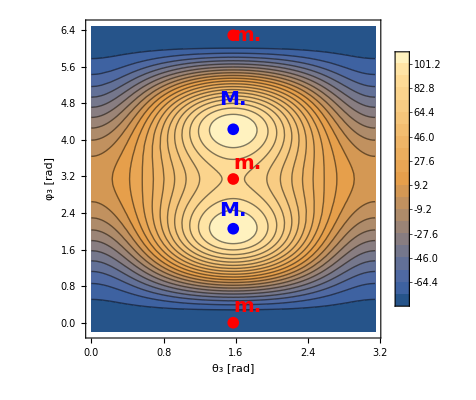

```mathematica
cp[19/2]
```

## Numerical test for Energies: the cases of minimal/maximal points on 3-axis quantization

```mathematica
testEmax[I_,v_]:=N[I^2(1+v^2)];
testEmin[I_,v_]:=N[-2*v*I];
Print[testEmax[19/2,v0fct[19/2,IF[30],IF[15],j11,-11*π/180]],"\n",testEmin[19/2,v0fct[19/2,IF[30],IF[15],j11,-11*π/180]]]
```

1854.98
84.0175

```mathematica
N[Hen[19/2,IF[30],IF[15],IF[60],j11,-11*π/180,π/2,maximum[19/2,30,15,60,11/2,-11,0,3]]]
```

109.804